# Appendix D, nutrient asymmetry model

This notebook is for the analysis of a nutrient asymmetry model, presented in appendix D

### Sets of parameters used

```mathematica
scenarioD = {W0 -> 1, a0-> 0.01, zb -> 10, r -> 0.5, l -> 0.05, b->0,  q0->0.045, qmin-> 0.005, p->1,h->0.1, Nu0->5, w->0.2, u->5 }
```

{W0→1,a0→0.01,zb→10,r→0.5,l→0.05,b→0,q0→0.045,qmin→0.005,p→1,h→0.1,Nu0→5,w→0.25}

### Model equations

```mathematica
grS = (r S (n/(n+h)) (1/(1+ a[z,z] S + W[z])) - l S )/.{n -> Nu[z]/(1+q[z,z] S)}//FullSimplify
```

-l S+(√2 Nu0 r S)/((√2 Nu0+2 ⅇ^((z-zb)^2/(2 u^2)) h √π (1+(q0+qmin) S) u) (1+a0 S+(-1+ⅇ^(w z)) W0))

```mathematica
reseq = Solve[grS ==0, S]
```

{{S→0},{S→(√2 a0 l Nu0+2 a0 ⅇ^((z-zb)^2/(2 u^2)) h l √π u+2 ⅇ^((z-zb)^2/(2 u^2)) h l √π q0 u+2 ⅇ^((z-zb)^2/(2 u^2)) h l √π qmin u+2 ⅇ^(w z+(z-zb)^2/(2 u^2)) h l √π q0 u W0-2 ⅇ^((z-zb)^2/(2 u^2)) h l √π q0 u W0+2 ⅇ^(w z+(z-zb)^2/(2 u^2)) h l √π qmin u W0-2 ⅇ^((z-zb)^2/(2 u^2)) h l √π qmin u W0-√(-4 (-2 a0 ⅇ^((z-zb)^2/(2 u^2)) h l √π q0 u-2 a0 ⅇ^((z-zb)^2/(2 u^2)) h l √π qmin u) (-√2 l Nu0+√2 Nu0 r-2 ⅇ^((z-zb)^2/(2 u^2)) h l √π u+√2 l Nu0 W0-√2 ⅇ^(w z) l Nu0 W0-2 ⅇ^(w z+(z-zb)^2/(2 u^2)) h l √π u W0+2 ⅇ^((z-zb)^2/(2 u^2)) h l √π u W0)+(-√2 a0 l Nu0-2 a0 ⅇ^((z-zb)^2/(2 u^2)) h l √π u-2 ⅇ^((z-zb)^2/(2 u^2)) h l √π q0 u-2 ⅇ^((z-zb)^2/(2 u^2)) h l √π qmin u-2 ⅇ^(w z+(z-zb)^2/(2 u^2)) h l √π q0 u W0+2 ⅇ^((z-zb)^2/(2 u^2)) h l √π q0 u W0-2 ⅇ^(w z+(z-zb)^2/(2 u^2)) h l √π qmin u W0+2 ⅇ^((z-zb)^2/(2 u^2)) h l √π qmin u W0)^2))/(2 (-2 a0 ⅇ^((z-zb)^2/(2 u^2)) h l √π q0 u-2 a0 ⅇ^((z-zb)^2/(2 u^2)) h l √π qmin u))},{S→(√2 a0 l Nu0+2 a0 ⅇ^((z-zb)^2/(2 u^2)) h l √π u+2 ⅇ^((z-zb)^2/(2 u^2)) h l √π q0 u+2 ⅇ^((z-zb)^2/(2 u^2)) h l √π qmin u+2 ⅇ^(w z+(z-zb)^2/(2 u^2)) h l √π q0 u W0-2 ⅇ^((z-zb)^2/(2 u^2)) h l √π q0 u W0+2 ⅇ^(w z+(z-zb)^2/(2 u^2)) h l √π qmin u W0-2 ⅇ^((z-zb)^2/(2 u^2)) h l √π qmin u W0+√(-4 (-2 a0 ⅇ^((z-zb)^2/(2 u^2)) h l √π q0 u-2 a0 ⅇ^((z-zb)^2/(2 u^2)) h l √π qmin u) (-√2 l Nu0+√2 Nu0 r-2 ⅇ^((z-zb)^2/(2 u^2)) h l √π u+√2 l Nu0 W0-√2 ⅇ^(w z) l Nu0 W0-2 ⅇ^(w z+(z-zb)^2/(2 u^2)) h l √π u W0+2 ⅇ^((z-zb)^2/(2 u^2)) h l √π u W0)+(-√2 a0 l Nu0-2 a0 ⅇ^((z-zb)^2/(2 u^2)) h l √π u-2 ⅇ^((z-zb)^2/(2 u^2)) h l √π q0 u-2 ⅇ^((z-zb)^2/(2 u^2)) h l √π qmin u-2 ⅇ^(w z+(z-zb)^2/(2 u^2)) h l √π q0 u W0+2 ⅇ^((z-zb)^2/(2 u^2)) h l √π q0 u W0-2 ⅇ^(w z+(z-zb)^2/(2 u^2)) h l √π qmin u W0+2 ⅇ^((z-zb)^2/(2 u^2)) h l √π qmin u W0)^2))/(2 (-2 a0 ⅇ^((z-zb)^2/(2 u^2)) h l √π q0 u-2 a0 ⅇ^((z-zb)^2/(2 u^2)) h l √π qmin u))}}

### Feasibility conditions

Under which conditions are each equilibria feasible ? 
Since every parameter is positive, the third solution is necessarily negative. 
In the second solution, what is inside the square root has to be positive for the macrophyte population to be real, which is the case when :

```mathematica
Solve[(-h l-l Nu+r Nu-h l W-l Nu W)==0, Nu]//FullSimplify
```

{{Nu→-(h l (1+W))/(l-r+l W)}}

Since Nu is a quantity of nutrient it also has to be positive, which is the case when r>l(1+W).
The feasibility conditions are :  Nu > h l (1 + W) / (r - l (1+W)),  r>l(1+W).

### Invasion fitness

The invasion fitness of the mutant can be written as :

```mathematica
invasionFitness = (r (n/(n+h)) (1/(1+ a[zm,z] Seq + W[zm])) - l)/.{n-> Nu[zm]/(1+q[zm,z] Seq)}//Simplify
```

-l+(√2 (1+ⅇ^(p (z-zm))) (1+ⅇ^(b (-z+zm))) Nu0 r)/((√2 (1+ⅇ^(p (z-zm))) Nu0+2 ⅇ^((zb-zm)^2/(2 u^2)) h √π (1+qmin Seq+ⅇ^(p (z-zm)) (1+2 q0 Seq+qmin Seq)) u) (1+ⅇ^(b (-z+zm)) (1+2 a0 Seq-W0)-W0+ⅇ^(w zm) W0+ⅇ^(w zm+b (-z+zm)) W0))

Assuming that the resident has reached equilibrium, it becomes:

```mathematica
invasionFitness = invasionFitness/.{Seq -> S/.reseq[[2]]}
```

-l+(√2 (1+ⅇ^(p (z-zm))) (1+ⅇ^(b (-z+zm))) Nu0 r)/((1-W0+ⅇ^(w zm) W0+ⅇ^(w zm+b (-z+zm)) W0+ⅇ^(b (-z+zm)) (1-W0+(a0 (√2 a0 l Nu0+2 a0 ⅇ^((z-zb)^2/(2 u^2)) h l √π u+2 ⅇ^((z-zb)^2/(2 u^2)) h l √π q0 u+2 ⅇ^((z-zb)^2/(2 u^2)) h l √π qmin u+2 ⅇ^(w z+(z-zb)^2/(2 u^2)) h l √π q0 u W0-2 ⅇ^((z-zb)^2/(2 u^2)) h l √π q0 u W0+2 ⅇ^(w z+(z-zb)^2/(2 u^2)) h l √π qmin u W0-2 ⅇ^((z-zb)^2/(2 u^2)) h l √π qmin u W0-√(-4 (-2 a0 ⅇ^((z-zb)^2/(2 u^2)) h l √π q0 u-2 a0 ⅇ^((z-zb)^2/(2 u^2)) h l √π qmin u) (-√2 l Nu0+√2 Nu0 r-2 ⅇ^((z-zb)^2/(2 u^2)) h l √π u+√2 l Nu0 W0-√2 ⅇ^(w z) l Nu0 W0-2 ⅇ^(w z+(z-zb)^2/(2 u^2)) h l √π u W0+2 ⅇ^((z-zb)^2/(2 u^2)) h l √π u W0)+(-√2 a0 l Nu0-2 a0 ⅇ^((z-zb)^2/(2 u^2)) h l √π u-2 ⅇ^((z-zb)^2/(2 u^2)) h l √π q0 u-2 ⅇ^((z-zb)^2/(2 u^2)) h l √π qmin u-2 ⅇ^(w z+(z-zb)^2/(2 u^2)) h l √π q0 u W0+2 ⅇ^((z-zb)^2/(2 u^2)) h l √π q0 u W0-2 ⅇ^(w z+(z-zb)^2/(2 u^2)) h l √π qmin u W0+2 ⅇ^((z-zb)^2/(2 u^2)) h l √π qmin u W0)^2)))/(-2 a0 ⅇ^((z-zb)^2/(2 u^2)) h l √π q0 u-2 a0 ⅇ^((z-zb)^2/(2 u^2)) h l √π qmin u))) (√2 (1+ⅇ^(p (z-zm))) Nu0+2 ⅇ^((zb-zm)^2/(2 u^2)) h √π u (1+(qmin (√2 a0 l Nu0+2 a0 ⅇ^((z-zb)^2/(2 u^2)) h l √π u+2 ⅇ^((z-zb)^2/(2 u^2)) h l √π q0 u+2 ⅇ^((z-zb)^2/(2 u^2)) h l √π qmin u+2 ⅇ^(w z+(z-zb)^2/(2 u^2)) h l √π q0 u W0-2 ⅇ^((z-zb)^2/(2 u^2)) h l √π q0 u W0+2 ⅇ^(w z+(z-zb)^2/(2 u^2)) h l √π qmin u W0-2 ⅇ^((z-zb)^2/(2 u^2)) h l √π qmin u W0-√(-4 (-2 a0 ⅇ^((z-zb)^2/(2 u^2)) h l √π q0 u-2 a0 ⅇ^((z-zb)^2/(2 u^2)) h l √π qmin u) (-√2 l Nu0+√2 Nu0 r-2 ⅇ^((z-zb)^2/(2 u^2)) h l √π u+√2 l Nu0 W0-√2 ⅇ^(w z) l Nu0 W0-2 ⅇ^(w z+(z-zb)^2/(2 u^2)) h l √π u W0+2 ⅇ^((z-zb)^2/(2 u^2)) h l √π u W0)+(-√2 a0 l Nu0-2 a0 ⅇ^((z-zb)^2/(2 u^2)) h l √π u-2 ⅇ^((z-zb)^2/(2 u^2)) h l √π q0 u-2 ⅇ^((z-zb)^2/(2 u^2)) h l √π qmin u-2 ⅇ^(w z+(z-zb)^2/(2 u^2)) h l √π q0 u W0+2 ⅇ^((z-zb)^2/(2 u^2)) h l √π q0 u W0-2 ⅇ^(w z+(z-zb)^2/(2 u^2)) h l √π qmin u W0+2 ⅇ^((z-zb)^2/(2 u^2)) h l √π qmin u W0)^2)))/(2 (-2 a0 ⅇ^((z-zb)^2/(2 u^2)) h l √π q0 u-2 a0 ⅇ^((z-zb)^2/(2 u^2)) h l √π qmin u))+ⅇ^(p (z-zm)) (1+(q0 (√2 a0 l Nu0+2 a0 ⅇ^((z-zb)^2/(2 u^2)) h l √π u+2 ⅇ^((z-zb)^2/(2 u^2)) h l √π q0 u+2 ⅇ^((z-zb)^2/(2 u^2)) h l √π qmin u+2 ⅇ^(w z+(z-zb)^2/(2 u^2)) h l √π q0 u W0-2 ⅇ^((z-zb)^2/(2 u^2)) h l √π q0 u W0+2 ⅇ^(w z+(z-zb)^2/(2 u^2)) h l √π qmin u W0-2 ⅇ^((z-zb)^2/(2 u^2)) h l √π qmin u W0-√(-4 (-2 a0 ⅇ^((z-zb)^2/(2 u^2)) h l √π q0 u-2 a0 ⅇ^((z-zb)^2/(2 u^2)) h l √π qmin u) (-√2 l Nu0+√2 Nu0 r-2 ⅇ^((z-zb)^2/(2 u^2)) h l √π u+√2 l Nu0 W0-√2 ⅇ^(w z) l Nu0 W0-2 ⅇ^(w z+(z-zb)^2/(2 u^2)) h l √π u W0+2 ⅇ^((z-zb)^2/(2 u^2)) h l √π u W0)+(-√2 a0 l Nu0-2 a0 ⅇ^((z-zb)^2/(2 u^2)) h l √π u-2 ⅇ^((z-zb)^2/(2 u^2)) h l √π q0 u-2 ⅇ^((z-zb)^2/(2 u^2)) h l √π qmin u-2 ⅇ^(w z+(z-zb)^2/(2 u^2)) h l √π q0 u W0+2 ⅇ^((z-zb)^2/(2 u^2)) h l √π q0 u W0-2 ⅇ^(w z+(z-zb)^2/(2 u^2)) h l √π qmin u W0+2 ⅇ^((z-zb)^2/(2 u^2)) h l √π qmin u W0)^2)))/(-2 a0 ⅇ^((z-zb)^2/(2 u^2)) h l √π q0 u-2 a0 ⅇ^((z-zb)^2/(2 u^2)) h l √π qmin u)+(qmin (√2 a0 l Nu0+2 a0 ⅇ^((z-zb)^2/(2 u^2)) h l √π u+2 ⅇ^((z-zb)^2/(2 u^2)) h l √π q0 u+2 ⅇ^((z-zb)^2/(2 u^2)) h l √π qmin u+2 ⅇ^(w z+(z-zb)^2/(2 u^2)) h l √π q0 u W0-2 ⅇ^((z-zb)^2/(2 u^2)) h l √π q0 u W0+2 ⅇ^(w z+(z-zb)^2/(2 u^2)) h l √π qmin u W0-2 ⅇ^((z-zb)^2/(2 u^2)) h l √π qmin u W0-√(-4 (-2 a0 ⅇ^((z-zb)^2/(2 u^2)) h l √π q0 u-2 a0 ⅇ^((z-zb)^2/(2 u^2)) h l √π qmin u) (-√2 l Nu0+√2 Nu0 r-2 ⅇ^((z-zb)^2/(2 u^2)) h l √π u+√2 l Nu0 W0-√2 ⅇ^(w z) l Nu0 W0-2 ⅇ^(w z+(z-zb)^2/(2 u^2)) h l √π u W0+2 ⅇ^((z-zb)^2/(2 u^2)) h l √π u W0)+(-√2 a0 l Nu0-2 a0 ⅇ^((z-zb)^2/(2 u^2)) h l √π u-2 ⅇ^((z-zb)^2/(2 u^2)) h l √π q0 u-2 ⅇ^((z-zb)^2/(2 u^2)) h l √π qmin u-2 ⅇ^(w z+(z-zb)^2/(2 u^2)) h l √π q0 u W0+2 ⅇ^((z-zb)^2/(2 u^2)) h l √π q0 u W0-2 ⅇ^(w z+(z-zb)^2/(2 u^2)) h l √π qmin u W0+2 ⅇ^((z-zb)^2/(2 u^2)) h l √π qmin u W0)^2)))/(2 (-2 a0 ⅇ^((z-zb)^2/(2 u^2)) h l √π q0 u-2 a0 ⅇ^((z-zb)^2/(2 u^2)) h l √π qmin u))))))

### Specification of the functions used

Mechanism 1: vertical trade-off between light and nutrient

```mathematica
Nu[x_]:=(Nu0/(u* Sqrt[2 * Pi])) * Exp[-(zb-x)^2/(2u^2)]
```

```mathematica
W[x_]:=  W0 Exp[w x] - W0
```

Mechanism 2: asymmetric competition by shading

```mathematica
a[x_,y_] := (a0 2 Exp[ b (x-y)] / (1 +  Exp[b (x-y)]))
```

Mechanism 3: asymmetric competition fro nutrient

```mathematica
q[x_, y_] := ((q0 2 Exp [p(-(x-y))]/(1 + Exp[p(-(x-y))])) + qmin)
```

### Feasibility set of parameters

Recall that Nu needs to be greater than  h l (1 + W) / (r - l (1+W)). 
We can test : 		Nu - h l (1 + W) / (r - l (1+W)) > 0  with  (r - l (1+W)) > 0 
or , since Nu >0, 	0 < (h l (1 + W) / (r - l (1+W)))/Nu < 1

```mathematica
feasibilityCondition =(h l (1 + W[z]) / (r - l (1+W[z])))/Nu[z]
```

(ⅇ^((-z+zb)^2/(2 u^2)) h l √(2 π) u (1-W0+ⅇ^(w z) W0))/(Nu0 (r-l (1-W0+ⅇ^(w z) W0)))

## PIPs

This section of the file generates the PIPs presented in Fig. 3 and can be used to generate others with different sets of parameters.

```mathematica
base = ContourPlot[z^2 + zm^2,{z,0,10},{zm,0,10}, Contours-> 0, ContourShading->{Blue},PlotPoints->5];
```

{z→-6.11294}

{z→8.26628}

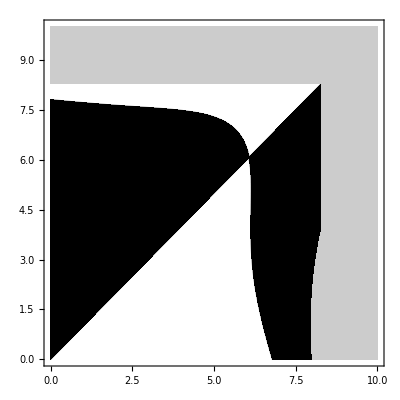

```mathematica
example = Join[scenarioD, {u->5, w->0.2}]; (*for strong light attenuation and little nutrient diffusion*)
zmin = FindRoot[((feasibilityCondition/.example)-1), {z,0}] (*find the boundaries of feasible depths*)
zmax = FindRoot[((feasibilityCondition/.example)-1), {z,10}]
If[(z/.zmin) < 0, zmin = 0, zmin = (z/.zmin)];
If[(z/.zmax) > 10, zmax = 10, zmax= (z/.zmax)];
plot = ContourPlot[invasionFitness/.example,{z,zmin,zmax},{zm,zmin,zmax}, Contours-> {0}, ContourShading->{White, Black},PlotPoints->50]; (*draw the PIP in the feasible depths - black regions correspond to a positive invasion fitness, white regions to negative invasion fitness*)
Show[base,plot]
```

## Evolutionary singularity analysis

### What is the value of the evolutionary singularity ?

For which z does ds/dzm (z, z) = 0 ?

```mathematica
dsdzm = D[invasionFitness, zm] ;
```

### Is the singularity non-invasible ?

<-> d2s/dzm2 (z*, z*) < 0 ?

```mathematica
stabilityCondition = D[dsdzm, zm]/.{z -> ES, zm -> ES};
```

### Is the equilibrium attractive ?

<-> d2s/dzm2(z*,z*) + d2s/dzdzm(z*,z*) <0

```mathematica
secondPart =  D[invasionFitness, z] ;
```

```mathematica
secondPart = D[secondPart, zm];
```

```mathematica
secondPart = secondPart/.{z -> ES, zm -> ES};
```

```mathematica
attractivityCondition = stabilityCondition + secondPart
```

0.-1/(1^2 1)+25
 |  |  |  |

## Obtaining values for E3 diagrams or 2D plots

This part of the file computes the value of the evolutionary singularity and classifies it according to convergence and invasibility criteria for a range of nutrient diffusion u and light attenuation w values. The output is written in a txt file in the data/ directory.

```mathematica
filename = ParentDirectory[NotebookDirectory[]]<>"/data/evolution_scenario3_appendix.txt";(*or scenario2 or scenario3*)
```

```mathematica
file = OpenWrite[filename, FormatType->StandardForm]
```

OutputStream[…]

```mathematica
pars = scenarioD
```

{W0→1,a0→0.01,zb→10,r→0.5,l→0.05,b→0,q0→0.045,qmin→0.005,p→1,h→0.1,Nu0→5,w→0.25}

```mathematica
Write[file, "#"<>ToString[pars]]
```

```mathematica
Write[file, "p, zmin, zmax, ES, type"]
```

```mathematica
Do[
(*find the feasibility range: 
- is there an upper-bound and a lower bound, or only one, or no bound? *)
lim= z/.FindRoot[((feasibilityCondition/.pars)-1), {z,#}]&/@Range[10];
lim=N[Round[1000000 lim ]/1000000];
lim=DeleteDuplicates[lim];
lim=DeleteCases[lim, x_ /; (x<0 ||  x>10) ];
If[Length[lim]==2,zmin=lim[[1]]; zmax=lim[[2]] ];
If [Length[lim]==0,zmin=0; zmax=10];(*This can also possilby be that life is possible nowhere (but that case is delt with below)*)
If [Length[lim]==1,If[(((feasibilityCondition/.pars)-1)/.{z -> lim-1})[[1]]<0,zmax=lim[[1]];zmin=0, zmin=lim[[1]];zmax=10]];

ES = z/.(FindRoot[dsdzm/.pars/.{zm -> z},{z,zmin}]); (*compute the evolutionary singularity*)
(*Classify the evolutionary singularity :*) 
If[(feasibilityCondition/.pars/.{z->ES}) < 0 || (feasibilityCondition/.pars/.{z->ES}) >1, eType= "Unfeasible",
If[ES> zmin &&ES<zmax,

	If[((attractivityCondition/.pars) < 0  )&& ((stabilityCondition/.pars)< 0 ), 
	eType = "CSS"];
	If[((attractivityCondition/.pars) < 0  )&& ((stabilityCondition/.pars)> 0 ),
	eType = "Branching point"];
	If[((attractivityCondition/.pars) > 0  )&& ((stabilityCondition/.pars)> 0 ), 
	eType ="Repellor"];
	If[((attractivityCondition/.pars) > 0  )&& ((stabilityCondition/.pars)< 0 ), 
	eType ="Garden of Eden"],
 eType="No ES"]];
(*if there is no evolutionary singularity (lines in the PIP do not cross), does the macrophyte population evolve towards the bottom or the surface of the lake ? : *)
If[eType=="No ES", If[(invasionFitness/.pars/.{z->0,zm->0.001})<0,ES=zmin,ES=zmax]];
Write[file,p,"," , zmin,"," ,zmax,"," ,ES,"," ,eType];

, {p,0,5,0.05}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

$Aborted

```mathematica
Close[file];
```